```mathematica
Ln1=4;
Ln2=1;
c=1;
```

P(l1<L1, l2< L2)

```mathematica
P1[l1_,l2_,c_,γ_]:=((l1+l2+c-1)!)/((c-1)!l1!l2!)*(1/(2+γ))^(l1+l2)(γ/(2+γ))^c
```

P(l1<L1,l2=L2)

```mathematica
P2[l1_,L2_,c_,γ_]:=((l1+c-1)!)/(l1!(c-1)!)*γ^c/(γ+1)^(l1+c)-Sum[((l1+l2+c-1)!)/((c-1)!l1!l2!)*γ^c/(γ+2)^(l1+l2+c),{l2,0,L2-1}]
```

P(l1=L1,l2=L2). First term is all structures l1=(0-L1-1), l2=(0:L2). Second term is l1=L1, l2=L2-1. Note that L1 cannot be less than 1.

```mathematica
P3[L1_,L2_,c_,γ_]:=1-Sum[Sum[P1[l1,l2,c,γ],{l1,0,L1-1}],{l2,0,L2-1}]-Sum[P2[l1,L2,c,γ],{l1,0,L1-1}]-Sum[P2[l2,L1,c,γ],{l2,0,L2-1}]
```

Marginals (l1<L1) (Change l2 for l1 to get the opposite)

```mathematica
PM1[l1_,L2_,c_,γ_]:=Sum[P1[l1,l2,c,γ],{l2,0,L2-1}]+P2[l1,L2,c,γ]
PM1[l1,l2,1,γ]
```

Marginals (l=L) (l2=L2) (Change l1 for l2 to get opposite)

```mathematica
PM2[L1_,L2_,c_,γ_]:=Sum[P2[l1,L2,c,γ],{l1,0,L1-1}]+P3[L1,L2,c,γ]
```

Mutual Information

```mathematica
IN[L1_,L2_,c_,γ_]:=Sum[Sum[P1[l1,l2,c,γ]*Log[P1[l1,l2,c,γ]/(PM1[l1,L2,c,γ]*PM1[l2,L1,c,γ])],{l1,0,L1-1}],{l2,0,L2-1}]+Sum[P2[l1,L2,c,γ]*Log[P2[l1,L2,c,γ]/(PM1[l1,L2,c,γ]*PM2[L1,L2,c,γ])],{l1,0,L1-1}]+Sum[P2[l2,L1,c,γ]*Log[P2[l2,L1,c,γ]/(PM1[l2,L1,c,γ]*PM2[L2,L1,c,γ])],{l2,0,L2-1}]+P3[L1,L2,c,γ]*Log[P3[L1,L2,c,γ]/(PM2[L1,L2,c,γ]*PM2[L2,L1,c,γ])]
```

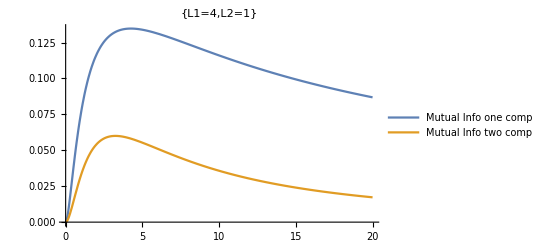

```mathematica
Plot[{IN[4,1,1,1/τ],IN[4,1,2,2/τ]},{τ,0,20},PlotLabel->{"L1=4,L2=1"}, PlotLegends->{"Mutual Info one comp","Mutual Info two comp"}]
```